```mathematica
sheet[x_,p_,w_,g_]:=(Tanh[2(x-p+w/2)/g]-Tanh[2(x-p-w/2)/g])/2
```

```mathematica
Q[x_,c_,oh_,ol_,ah_,al_,f_,wh_,wl_,gh_,gl_]:=(ah-al)sheet[x,c+oh,wh,gh]+(al-f)sheet[x,c+ol,wl,gl]+f
FullSimplify[D[Normal[Series[Q[x,c,oh,ol,ah,al,f,wh,wl,gh,gl],{x,#,1}]],x]/.wh->∞/.wl->∞,Assumptions->{gh>0,gl>0}]&/@{c+ol-wl/2,c+ol+wl/2,c+oh-wh/2,c+oh+wh/2}
```

{(al-f)/gl,(-al+f)/gl,(ah-al)/gh,(-ah+al)/gh}

```mathematica
E0[x_,c_,oh_,ol_,ah_,al_,f_,wh_,wl_,gh_,gl_]:=(ah-al)sheet[x,c+oh,wh,gh]+(al-f)sheet[x,c+ol,wl,gl]+f
FullSimplify[D[Normal[Series[E0[x,c,oh,ol,ah,al,f,wh,wl,gh,gl],{x,#,1}]],x]/.wh->∞/.wl->∞,Assumptions->{gh>0,gl>0}]&/@{c+ol-wl/2,c+ol+wl/2,c+oh-wh/2,c+oh+wh/2}
```

{(al-f)/gl,(-al+f)/gl,(ah-al)/gh,(-ah+al)/gh}

```mathematica
J[x_,c_,a_,w_,g_,r_]:=a(sheet[x,c+w/2,w,g]-sheet[x,c-r w/2,r w,g]/r)
FullSimplify[D[Normal[Series[J[x,c,a,w,g,r],{x,#,1}]],x]/.w->∞,Assumptions->{a>0,g>0,r>0}]&/@{c-r w,c,c+w}
```

{-a/(g r),(a (1+r))/(g r),-a/g}

```mathematica
F[x_,c_,a_,w_,g_,r_]:=a(1/4 g Log[Cosh[(2 (c-x))/g]]+(g Log[Cosh[(2 (c-x))/g]])/(4 r)-1/4 g Log[Cosh[(2 (c+w-x))/g]]-(g Log[Cosh[(2 (c-r w-x))/g]])/(4 r))
```

```mathematica
Manipulate[
Plot[{
J[x,c,Ka/Jw,Jw,Jg,Jr] 10^6
,(Ka/(2 Jw)-(c Ka)/(Jg Jw)-Ka/(2 Jr Jw)-(c Ka)/(Jg Jr Jw)+(Ka x)/(Jg Jw)+(Ka x)/(Jg Jr Jw))10^6
,(Ka/Jg+Ka/(2 Jw)+(c Ka)/(Jg Jw)-(Ka x)/(Jg Jw))10^6
,(-Ka/Jg-Ka/(2 Jr Jw)+(c Ka)/(Jg Jr Jw)-(Ka x)/(Jg Jr Jw))10^6
,Q[x,c,Qoh,Qol,Qah,Qal,Qf,Qwh,Qwl,Qgh,Qgl]
,E0[x,c,Qoh,Qol,Eah,Eal,Ef,Ewh,Ewl,Egh,Egl] 10^-3
,Q[x,c,Qoh,Qol,Qah,Qal,Qf,Qwh,Qwl,Qgh,Qgl]/E0[x,c,Qoh,Qol,Eah,Eal,Ef,Ewh,Ewl,Egh,Egl]/2 10^-3/(1.60218 10^-19)10^-13(*10^13/s/m^2*)
,F[x,c,Ka/Jw,Jw,Jg,Jr](40 E0[x,c,Qoh,Qol,Eah,Eal,Ef,Ewh,Ewl,Egh,Egl] 10^-3)/(16+E0[x,c,Qoh,Qol,Eah,Eal,Ef,Ewh,Ewl,Egh,Egl] 10^-3) Q[x,c,Qoh,Qol,Qah,Qal,Qf,Qwh,Qwl,Qgh,Qgl]^(1/2)
},{x,-350000,350000},PlotRange->{All,{-4,4}}
,GridLines->{{
c-Jw Jr-Jg/2
,c-Jw Jr+Jg/2
,c+Jg/2
,c-Jg/2
,c+Jw-Jg/2
,c+Jw+Jg/2
},{-Ka/Jw/Jr 10^6,Ka/Jw 10^6}}
,AspectRatio->0.6
,ImageSize->Full
,PlotStyle->{Red,{Red,Dashed},{Red,Dashed},{Red,Dashed},Blue,{Blue,Dashed},Cyan,Magenta}
]
,{{c,0},-400000,400000}
,{{Qah,6},1,10}
,{{Qal,2},1,10}
,{{Qwh,20000},10000,50000}
,{{Qwl,200000},100000,500000}
,{{Qgh,5000},5000,50000}
,{{Qgl,40000},5000,50000}
,{{Qoh,100000},0,200000}
,{{Qol,150000},0,200000}
,{{Qf,0.3},0,1}
,{{Eah,4000},2000,10000}
,{{Eal,2000},2000,10000}
,{{Ewh,20000},10000,50000}
,{{Ewl,200000},100000,500000}
,{{Egh,5000},5000,50000}
,{{Egl,40000},5000,50000}
,{{Ef,1500},0,2000}
,{{Ka,0.3},0.1,0.5}
,{{Jw,300000},100000,300000}
,{{Jg,40000},5000,50000}
,{{Jr,1/2},0.1,1}
,{{Fa,1000},500,5000}
]
```

```mathematica
40
```

```mathematica
F[c,c,a,w,g,r]
```

a (-1/4 g Log[Cosh[(2 w)/g]]-(g Log[Cosh[(2 r w)/g]])/(4 r))

```mathematica
qtot[Q_,E0_]:=Module[{
P
,kB=1.38064852 10^-16(*cm^2 g s^-2 K^-1*)
,G=6.67408 10^-8(*cm^3 g^-1 s^-2*)
,ME=5.9722 10^24 10^3(*g*)
,RE=6.371 10^6 10^2(*cm*)
,amu=1.660539040 10^-27 10^3(*g*)
,Δϵ=35 10^-3(*keV*)
,erg2kev=6.24150648 10^8
,msis
,z
,g
,n
,m
,T
,H
,ρ
,y
,q
},
P={{3.49979 10^(−1 ),−6.18200 10^(−2 ),−4.08124 10^(−2 ), 1.65414 10^(−2 )},
{5.85425 10^(−1 ),−5.00793 10^(−2 ), 5.69309 10^(−2 ),−4.02491 10^(−3 )},
{1.69692 10^(−1 ),−2.58981 10^(−2 ), 1.96822 10^(−2 ), 1.20505 10^(−3 )},
{-1.22271 10^(−1 ),−1.15532 10^(−2 ), 5.37951 10^(−6 ), 1.20189 10^(−3 )},
{1.57018 10^(0 ), 2.87896 10^(−1 ),−4.14857 10^(−1 ), 5.18158 10^(−2 )},
{8.83195 10^(−1 ), 4.31402 10^(−2 ),−8.33599 10^(−2 ), 1.02515 10^(−2 )},
{1.90953 10^(0 ),−4.74704 10^(−2 ),−1.80200 10^(−1 ), 2.46652 10^(−2 )},
{−1.29566 10^(0 ),−2.10952 10^(−1 ), 2.73106 10^(−1 ),−2.92752 10^(−2 )}};
c[i_]:=Exp[Sum[P[[i,j+1]](Log[E0])^j,{j,0,3}]];
f[y_]:=c[1] y^c[2] Exp[-c[3] y^c[4]]+c[5] y^c[6] Exp[-c[7] y^c[8]];
msis=ToExpression[StringSplit/@StringSplit[StringReplace[Import["D:\\Files\\research\\thesis\\msis_maeve_null.lst"],"E"->"*10^"],"
"][[43;;]]];
z=msis[[;;,3]] 10^3 10^2(*cm*);
g=(G ME)/(RE+z)^2(*cm s^-2*);
n=msis[[;;,{4,5,6,9,10,11,12}]](*cm^-3*);
ρ=msis[[;;,7]](*g cm^-3*);
m=ρ/(Total/@n) (*g*);
T=msis[[;;,8]](*K*);
H=k T/(m g)(*cm*);
y=1/E0((ρ H)/(4 10^-6))^0.606;
q=Log10[(Q erg2kev)/Δϵ 1/H f[y]];
Flatten[{z 10^-5,q}[[;;,Position[q,Max[q]][[1]]]]]

]
```

```mathematica
qtotmax=Table[{Log10[Q],E0,qtot[Q,E0][[1]],qtot[Q,E0][[2]]},{Q,1,100,5},{E0,2,10,1}];
```

```mathematica
ListPlot3D[Flatten[qtotmax[[;;,;;,{1,2,3}]],1]
,PlotLegends->BarLegend[Automatic,LegendLabel->"log_10(q_max)"]
,InterpolationOrder->0
,AxesLabel->{"Log_10 Q [erg cm^-2 s^-1]","E_0 [keV]","z_peak [km]"}
]
ListPlot3D[Flatten[qtotmax[[;;,;;,{1,2,4}]],1]
,PlotLegends->BarLegend[Automatic,LegendLabel->"log_10(q_max)"]
,InterpolationOrder->1
,AxesLabel->{"Log_10 Q [erg cm^-2 s^-1]","E_0 [keV]","Log_10 q_peak [cm^-3 s^-1]"}
]
```

-Graphics3D-

-Graphics3D-

```mathematica
ListLinePlot[Flatten[qtotmax[[;;,;;,{1,2,4}]],1]]
```

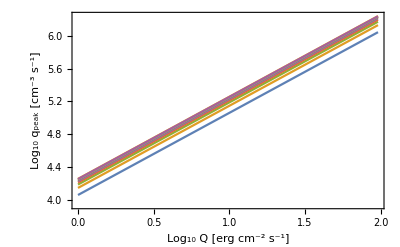

```mathematica
ListLinePlot[
Table[qtotmax[[;;,E0,{1,4}]],{E0,1,9,1}]
,Frame->True
,FrameLabel->{"Log_10 Q [erg cm^-2 s^-1]","Log_10 q_peak [cm^-3 s^-1]"}
]
```

```mathematica
Log10[50]//N
```

Log[50]/Log[10]